Perlin Noise is a procedural generation algorithm that creates pseudorandom values that can be used for the generation of realistic patterns. It takes in a 2D or 3D coordinate as an input and returns a random number in the range [-1, 1], although this range can be altered. With this algorithm, we can use it to create a realistic looking city by applying it to different aspects of a generation of a city.

## Introduction

### What is Perlin noise?

In computer graphics and game design, procedural generation offers a way to create vast and detailed worlds without having to hand-craft every element. One of the earliest and most influential tools for this is Perlin noise, an algorithm that is often used in terrain generation within video games, first published in 1985 by NYU professor Ken Perlin. 

The difference between Perlin noise and regular random noise is that while pure randomly generated noise can be chaotic and erratic, Perlin noise produces smooth, pseudo-random patterns that can be layered at different frequencies to mimic natural textures and terrain. It is useful in generating natural-looking randomness with specific desirable properties which makes it perfect for simulating natural-looking patterns, which in our case will be cities. One of the most popular examples of the use of Perlin noise is the terrain generation for the video game Minecraft.

In this project, we will be using Ken Perlin’s Improved Perlin Noise which he published in 2002.

## Creating Perlin Noise

NOTE: I would like to preface this section by mentioning that a lot of it is taken from this wonderful article by Flafla2. That article gives a C# version of the Improved Perlin Noise function. The original Improved Perlin Noise code is written in Java.

### Logical overview

Starting with the basic Perlin Noise function, for the input, we will take three coordinate parameters, {x,y,z} which will all be decimal coordinates and our output will be a decimal number between 0.0 and 1.0.

First we will divide the x, y, and z coordinates into unit cubes. 
This basically means that we will find [x,y,z]%1.0 to separate the decimal part of the coordinate in order to find the coordinate’s location within the 1x1 cube.

Visualizing this concept in 2 dimensions (only x and y):

-Graphics-

The blue dot represents an input coordinate and the four points making up the square are the surrounding integral unit coordinates.

On each of the 4 unit coordinates making up the square, we generate a pseudorandom gradient vector. The gradient vector defines a positive direction (the direction where the vector points to) and a negative direction (the direction opposite of where the vector points to). 
Pseudorandom means that the value given is deterministic and for any input given into the gradient vector equation, it will only give one kind of output. Although the output will seem random, it isn’t truly random. This also means that each integral coordinate has its “own” gradient that will never change if the gradient function doesn’t change.

Example of some gradient vectors:

-Graphics-

While the original Perlin Noise uses completely random gradients, in Ken Perlin’s Improved Noise, we will be using gradients picked from the vectors of the point in the center of a cube to the edges of the cube:

(1, 1, 0), (-1, 1, 0), (1, -1, 0), (-1, -1, 0),
(1, 0, 1), (-1, 0, 1), (1, 0, -1), (-1, 0, -1),
(0, 1, 1), (0, -1, 1), (0, 1, -1), (0, -1, -1)

The reason why the Improved Noise version does this is explained in this article.

After we pick our gradients, we need to calculate a distance vector from the four points to the given point.

Example of distance vectors:

-Graphics-

Next we take the dot product between the gradient vector and the distance vector. This will result in our final influence values.

Formula for the dot product between the gradient vector and distance vector:

grad.x * dist.x + grad.y * dist.y + grad.z * dist.z

This function is derived from the definition of a dot product which is the product of the magnitudes of 2 vectors multiplied with the cosine of the angle between the two vectors.

dot[vec1_, vec2_] := Cos[VectorAngle[vec1, vec2]] * vec1 // Norm * vec2 // Norm; (*Norm gets the magnitude of the vector*)

This will result in a positive value when the vectors are in the same direction and a negative value when the vectors are in opposite directions.
Here is an example of a visual representing the positive and negative influences

Visualization of influenced in 2D noise:

-Graphics-

Finally, we need to interpolate between these 4 values in order to get a weighted average between the 4 grid points.
We accomplish this by getting the average of the averages.

Assuming lerp[] is our linear interpolation function, g1, g2, g3, g4  are our dot product values, and  u, v are our coordinates of the location of the input coordinate its unit square(back when we did [x,y,z]%1.0), we get our weighted average by doing something like this:

x1 = lerp[g1, g2, u];
x2 = lerp[g3, g4, u];
average = lerp[x1, x2, v];

Our final step addresses one problem. The weighted average received above is not the best since linear interpolation often look unnatural. We can get a smoother transition between gradients by using a fade function(also called an ease curve).

Example of a fade function(ease curve):

-Graphics-

The Perlin Noise Function uses  as its fade function.

In our code, we will be doing all this in 3D which means that instead of having 4 points in our vector calculations, we will have 8 (cube has 8 vertices).

### Code Breakdown

#### Setup

The first thing to do is to set up a permutation table which we will call p[]. We will make an array of number 0-255 inclusive in a random order.

Creating a random permutation of the numbers 0-255. In order to avoid overflow, we will double the list.

permutation = RandomSample[Range[0, 255]];
p = Join[permutation, permutation];

To start off our perlin function, we need to decide a repeat value.

repeat = 255;

In this case, our noise will repeat and show patterns every 255 units we move our coordinates. We will use the Mod function to get the remainder so that if our input overflow over the repeat value, the modulo will keep it the coordinate between (-repeat,repeat).

While I will explain more about this later, the repeat value is mainly used to make the perlin noise repeat over values smaller than 256 because the perlin noise function will always repeat at least every 256 coordinates. In this project, the repeat value will not be relevant.

Perlin will take in x, y, and z coordinates. It will start by modding the values over the repeat value.

perlin[a_, b_, c_] := Module[
  {x = a, y = b, z = c},
  
  If[repeat > 0, { x = Mod[a, repeat], y = Mod[b, repeat], z = Mod[c, repeat]}]; 
  
  (*...*)
  ]

Next we need variables(xi, yi, zi) that will represent the unit cube that our coordinate is in. To first find the unit cube, we use the Floor function on each coordinate value. Then, we bind the coordinate values to the range [0,255] using modulo(remainder) over 256 so we won’t run into a Part error due to the index being too big when we access the p[] array. 

However instead of using Mod[x,256] to achieve this, the BitAnd function has the unique property of being able to do the same thing for any powers of 2 by inputting the power of 2 we want to mod by minus 1. 
This means that the following two lines of code will do the same thing:

Mod[x, 256]
BitAnd[x, 255]

If you would like to understand better on how this works, learn more about binary numbers and bit string flicking/bitwise operations.

This will the have the effect of Perlin noise repeating every 256 coordinates which is unfortunate if trying to use this for large maps. However, this problem can be fixed by simply using decimal coordinates since Perlin works with decimal coordinates. For example if we want to create a noise map 1000x1000 with no repeats, we can increment each coordinate by 0.1 so that the x, y, and z values used will only range [1,100].

We will then find the location of our coordinate inside the unit cube and assign these values to variables xf, yf, zf. This is essentially,  n=n%1.0 where n is a coordinate.

perlin[a_, b_, c_] := Module[
  {x = a, y = b, z = c, xi = BitAnd[Floor[a], 255], yi = BitAnd[Floor[b], 255], zi = BitAnd[Floor[c], 255], xf, yf, zf},
  
  (*..*)
  xf = x - Floor[x]; yf = y - Floor[y]; zf = z - Floor[z];  
  (*...*)
  ]

#### The Fade Function

The Perlin Noise Fade Function:


The Fade function, defined by Ken Perlin, eases coordinate values so that they will ease towards integral values. This ends up smoothing the final output.

We implement this in code as shown:

fade[t_] := t*t*t(t*(t*6-15)+10); (* THE FADE FUNCTION >:) *)

The fade function will be used on the coordinates inside the unit cube which we will save for interpolation later.

perlin[a_, b_, c_] := Module[
  {x = a, y = b, z = c, xi = BitAnd[Floor[a], 255], yi = BitAnd[Floor[b], 255], zi = BitAnd[Floor[c], 255], xf, yf, zf,u,v,w},
  
  (*..*)
  u=fade[xf];v=fade[yf];w=fade[zf];  
  (*...*)
  ]

#### The Hash Function

The Perlin Noise hash function is used to get a distinct value for every coordinate input.

The hash function is used outside of Perlin Noise and has other applications.

Defined by Wikipedia: “any function that can be used to map data of arbitrary size to data of fixed size, with slight differences in input data producing very big differences in output data.”

In our application of the hash function, we hash all 8 unit cube coordinates surrounding the input coordinate. 
We will create a helper function inc[] to increment the numbers and make sure the noise repeats.

inc[n_] := Module[{num = n+1}, If[repeat >0, num = Mod[num, repeat]]];

Note: our implementation of the hash function was increment each index/part by 1 since Wolfram lists start their index with 1.

Hash function inside the Perlin Noise Function:

perlin[a_, b_, c_] := Module[
  {x = a, y = b, z = c, xi = BitAnd[Floor[a], 255], yi = BitAnd[Floor[b], 255], zi = BitAnd[Floor[c], 255], xf, yf, zf, u, v, w, aaa, aba, aab, abb, baa, bba, bab, bbb},
  
  (*..*)
aaa=p[[p[[p[[    xi +1]]+    yi +1]]+    zi +1]];
aba=p[[p[[p[[    xi +1]]+inc[yi]+1]]+    zi +1]];
aab=p[[p[[p[[    xi +1]]+    yi +1]]+inc[zi]+1]];
abb=p[[p[[p[[    xi +1]]+inc[yi]+1]]+inc[zi]+1]];
baa=p[[p[[p[[inc[xi]+1]]+    yi +1]]+    zi +1]];
bba=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+    zi +1]];
bab=p[[p[[p[[inc[xi]+1]]+    yi +1]]+inc[zi]+1]];
bbb=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+inc[zi]+1]];
  (*...*)
  ]

This hash function gives a value between 0 and 255(inclusive) from our p[] array.

#### The Gradient Function

The goal of the gradient function is to calculate the dot product of a randomly selected gradient vector and the 8 location vectors.
To achieve this, we will pick a random vector from the 12 vectors given:

(1, 1, 0), (-1, 1, 0), (1, -1, 0), (-1, -1, 0),
(1, 0, 1), (-1, 0, 1), (1, 0, -1), (-1, 0, -1),
(0, 1, 1), (0, -1, 1), (0, 1, -1), (0, -1, -1)

This is determined by the last 4 bits of the hash function value (the first parameter of grad[]). The other 3 parameters represent the location vector (that will be used for the dot product).

Picks a random vector based on hash and returns the dot product:

grad[hash_, x_, y_, z_] := Module[{hashy = BitAnd[hash,15 ]}, 
Which[
hashy==0, x+y,
hashy==1, -x+y,
hashy==2, x-y,
hashy==3, -x-y,
hashy==4, x+z,
hashy==5, -x+z,
hashy==6, x-z,
hashy==7, -x-z,
hashy==8, y+z,
hashy==9, -y+z,
hashy==10, y-z,
hashy==11,-y-z,
hashy==12,y+x,
hashy==13,-y+z,
hashy==14,y-x,
hashy==15,-y-z]];

The original Perlin Noise code uses bit-flipping code to accomplish this.

#### Combining all the parts

We can now use all functions we defined above and use them for the 8 surrounding unit cube coordinates and interpolate them together

Linear Interpolate:

lerp[a_,b_,x_] :=a+x*(b-a);

We will use the variables x1, x2, y1, y2 in order to store the dot product between a pseudorandom gradient vector and the vector from the input coordinate to the 8 surrounding points in the unit cube.
We will then take the linear interpolation of all the values to get a weighted average based on the faded values we defined before(u, v, w).

Calculating the final noise value by getting the linear interpolation:

perlin[a_, b_, c_] := Module[
  {x = a, y = b, z = c, xi = BitAnd[Floor[a], 255], yi = BitAnd[Floor[b], 255], zi = BitAnd[Floor[c], 255], xf, yf, zf, u, v, w, aaa, aba, aab, abb, baa, bba, bab, bbb, x1, x2, y1, y2},
  
  (*..*)
x1 = lerp[grad[aaa,xf,yf,zf],grad[baa,xf-1,yf,zf], u];
x2 = lerp[grad[aba, xf, yf-1, zf], grad[bba, xf-1, yf-1, zf],u];
y1 = lerp[x1, x2, v];
x1 = lerp[grad[aab, xf, yf, zf-1], grad[bab, xf-1, yf, zf-1], u];
x2 = lerp[grad[abb, xf, yf-1, zf-1], grad[abb, xf, yf-1, zf-1], u];
y2 = lerp[x1, x2, v];
(lerp[y1, y2, w]+1)/2
  ]

The range that the Perlin Noise Function outputs is [-1,1], however to use it conveniently in our case, we will shift this range to [0,1] by adding 1 and dividing it by 2.

In the next section, we will put this all together:

### Final Perlin Noise function code

#### Initial values and helper functions:

```mathematica
permutation = RandomSample[Range[1, 256]];
p = Join[permutation, permutation]; 
repeat = 255;
fade[t_] := t*t*t*(t*(t*6-15)+10); (* THE FADE FUNCTION >:) *)
inc[n_] := Module[{num = n+1}, If[repeat >0, num = Mod[num, repeat]]];
grad[hash_, x_, y_, z_] := Module[{hashy = BitAnd[hash,15 ]}, 
Which[
hashy==0, x+y,
hashy==1, -x+y,
hashy==2, x-y,
hashy==3, -x-y,
hashy==4, x+z,
hashy==5, -x+z,
hashy==6, x-z,
hashy==7, -x-z,
hashy==8, y+z,
hashy==9, -y+z,
hashy==10, y-z,
hashy==11,-y-z,
hashy==12,y+x,
hashy==13,-y+z,
hashy==14,y-x,
hashy==15,-y-z]];
lerp[a_,b_,x_] :=a+x*(b-a);
```

#### Perlin Noise Function:

```mathematica
perlin[a_, b_, c_] := Module[{x=a, y=b, z=c,xi = BitAnd[Floor[a], 255], yi = BitAnd[Floor[b], 255], zi = BitAnd[Floor[c], 255],xf,yf,zf,u,v,w,aaa, aba, aab, abb, baa, bba, bab, bbb,x1,x2,y1,y2},If[repeat> 0,{ x = Mod[a, repeat], y = Mod[b, repeat], z = Mod[c, repeat]}];  
xf = x-Floor[x];yf = y-Floor[y];zf = z-Floor[z]; 
u = fade[xf]; v = fade[yf]; w = fade[zf];
aaa =p[[p[[p[[        xi   +1]]+yi+1]]+        zi    +1]]; aba = p[[p[[p[[xi+1]]+inc[yi]+1]]+zi+1]]; aab=p[[p[[p[[         xi   +1]]+yi+1]]+inc[zi]+1]]; abb=p[[p[[p[[xi+1]]+inc[yi]+1]]+inc[zi]+1]]; baa=p[[p[[p[[inc[xi]+1]]+yi+1]]+          zi  +1]]; bba=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+zi+1]]; bab=p[[p[[p[[inc[xi]+1]]+yi+1]]+inc[zi]+1]]; bbb=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+inc[zi]+1]];
x1 = lerp[grad[aaa,xf,yf,zf],grad[baa,xf-1,yf,zf], u];
x2 = lerp[grad[aba, xf, yf-1, zf], grad[bba, xf-1, yf-1, zf],u];
y1 = lerp[x1, x2, v];
x1 = lerp[grad[aab, xf, yf, zf-1], grad[bab, xf-1, yf, zf-1], u];
x2 = lerp[grad[abb, xf, yf-1, zf-1], grad[abb, xf, yf-1, zf-1], u];
y2 = lerp[x1, x2, v];
(lerp[y1, y2, w]+1)/2];
```

### Perlin Noise with Octaves

#### Explanation

One final issue with Perlin Noise is while it gives natural behavior too some extent, it looks too smooth. Often in reality, there are many small irregularities. For example cities aren’t always rows of rectangle blocks with streets of parallel lines. There are often slanted roads, circular roads, and varying sizes of blocks.

In order to fix this, we can use different octaves. This means that we take multiple noise functions with different frequencies and amplitudes and combine the values.
Frequency is the period the data is sampled.
Amplitude is the range that the result can be in.

Example of noises at different frequencies and amplitudes:

-Graphics-

Adding all these noises together:

-Graphics-

Each noise graph is called an octave of noise and each next octave has less and less influence on the final noise values.

In order to decide how much influence every next octave should have, we use a value called persistence. We use Hugo Elias’ definition of persistence.

Hugo Elias’ definition of persistence given i is the octave we calculate for:

frequency=2^i
amplitude=persistence^i

The implementation for this is shown below

#### Perlin Noise with Octaves code:

```mathematica
octavePerlin[x_,y_,z_,octaves_,persistence_]:=
Module[{total=0, frequency=1,amplitude=1,maxValue=0},
total = perlin[x*frequency,y*frequency,z*frequency]*amplitude + Total[Table[maxValue+= amplitude;amplitude*=persistence;frequency*=2;perlin[x*frequency,y*frequency,z*frequency]*amplitude, {i,octaves-1}]]; total/maxValue];
```

NOTE: The above explanation for Perlin Noise is simplified at times. For more a more in depth view of Perlin Code, you can check out Flafla2's article and also the source code.

### 3D demonstration

Using a 3D visual, we can see how Perlin Noise makes a much better random noise generator than simply using a random function.

Below is the map of a regular random map taking values in [0,1]

Map of random noise:

```mathematica
Plot3D[RandomReal[],{i,0,1},{j,0,1}]
```

-Graphics3D-

This is very ugly and would be horrible for natural generation of any sort :(.

Now we can try what a perlin map looks like. We will stay using 2 dimensional coordinates for now and set z=1 and map it in the coordinates [0,0] to [1,1].

Map of Perlin Noise at z =1 for [x,y] coordinates [0,0] to [1,1]:

```mathematica
Plot3D[perlin[x,y,1],{x,0,1},{y,0,1}]
```

-Graphics3D-

This looks much better :). However, we can make it better by adding a little random irregularities using octaves.

For this example, we will set z=1 and go through coordinates [0,0] to [1,1] again. We will use 6 octaves and a persistence value of 0.6.

Map of Perlin Noise using octaves with z=1, octaves = 6, persistence = 0.6. for the [x,y] coordinates [0,0] to [1,1]

```mathematica
Plot3D[octavePerlin[x,y,1,6,0.6],{x,0,1},{y,0,1}]
```

-Graphics3D-

This is great for generation since it has smooth transitions between the values while still having a little random regularities :D.

## Street structure generation

### World settings

To start creating our city, we will start by defining the settings. 
This includes:

width

height

the minimum size of each block

the maximum amount of jitter we get when placing our streets

the width of the roads

```mathematica
worldWidth=250;
worldHeight=250;
minBlock=15;
maxJitter=5;
roadWidth=5;
noiseFreq=0.1;
lowCutoff=0.2;
highCutoff=0.8;
mapGrid=Table[0,{x,worldWidth},{y,worldHeight}];
```

To start off the city’s structure, we start with a 2D array of 0s. This grid will be the floor of our city, having blocks divided by roads/streets.

```mathematica
mapGrid=Table[0,{x,worldWidth},{y,worldHeight}];
```

### Street generation algorithm

Our generateRoads[] function uses recursive subdivision to create roads and Perlin Noise to introduce randomness to the density of roads in an area.

#### Code Explanation

For our street generation, we will use a couple different helper functions:

A smoothing function to interpolate between a low and high bound based on x:

smoothstep[low_,high_,x_]:=Module[{t},t=Clip[(x-low)/(high-low),{0,1}]; t*t*(3-2*t)];

It will also use some other simple functions.
jitter[max_] will get a random jitter value based on max_
clamp[val_,min_,max_] will makes sure that the closest value to val between min and max will be returned.
pickAxis[R_] will identify the direction of the road given

Given the city’s dimension, the generateRoads[] function will recursively start dividing the map in half in order to make the roads. Each time, it makes sure it is not making a block smaller then the minBlockSize. In order to avoid repetitively dividing the block in half every time, we use a random jitter value to offset the location of the road. Finally, before we even decide to place a road, we check the perlin noise function to make a decision whether to place a road or not every iteration.

```mathematica
smoothstep[low_,high_,x_]:=Module[{t},t=Clip[(x-low)/(high-low),{0,1}]; t*t*(3-2*t)];
 jitter[max_]:=RandomReal[{-max,max}];
 clamp[val_,min_,max_]:=Min[Max[val,min],max];
 pickAxis[R_]:=If[R[[3]]>R[[4]],"vertical","horizontal"];
```

```mathematica
generateRoads[worldWidth_,worldHeight_,minBlock_,maxJitter_,roadWidth_,noiseFreq_,lowCutoff_,highCutoff_]:=Module[{stack={{0,0,worldWidth,worldHeight}},roads={},addVerticalRoad,addHorizontalRoad,pushChildren,roadAdded=False},
    
  addVerticalRoad[x_,yStart_,yEnd_,width_]:=(AppendTo[roads,{Max[x, 1],Max[yStart, 1],Max[x, 1],yEnd,width}]; roadAdded=True);
  
  addHorizontalRoad[xStart_,y_,xEnd_,width_]:=(AppendTo[roads,{Max[xStart, 1],Max[y, 1],xEnd,Max[y, 1],width}]; roadAdded=True);
  
  pushChildren[R_,xSplit_,ySplit_,dir_]:=
   If[dir=="vertical",
    AppendTo[stack,{R[[1]],R[[2]],xSplit-R[[1]],R[[4]]}];
    AppendTo[stack,{xSplit,R[[2]],R[[3]]+R[[1]]-xSplit,R[[4]]}],
    AppendTo[stack,{R[[1]],R[[2]],R[[3]],ySplit-R[[2]]}];
    AppendTo[stack,{R[[1]],ySplit,R[[3]],R[[4]]+R[[2]]-ySplit}]
    ];

  While[Length[stack]>0,
   Module[{R,n,Psplit,dir,xSplit,ySplit, sizeFactor},
    R=First[stack];
    stack=Rest[stack];
    
    n=octavePerlin[R[[1]]+R[[3]]/2,R[[2]]+R[[4]]/2,0,4,0.5];
sizeFactor=Min[(R[[3]]/minBlock)+(R[[4]]/minBlock),2];
    Psplit=smoothstep[lowCutoff,highCutoff,n]*sizeFactor;
    If[RandomReal[]>Psplit,Continue[]];
    
    If[R[[3]]<2*minBlock||R[[4]]<2*minBlock,Continue[]];
    
    dir=pickAxis[R];
    
    If[dir=="vertical",
     xSplit=clamp[R[[1]]+R[[3]]/2+jitter[maxJitter],R[[1]]+minBlock,R[[1]]+R[[3]]-minBlock];
     addVerticalRoad[xSplit,R[[2]],R[[2]]+R[[4]],roadWidth];
     pushChildren[R,xSplit,Null,dir],
     ySplit=clamp[R[[2]]+R[[4]]/2+jitter[maxJitter],R[[2]]+minBlock,R[[2]]+R[[4]]-minBlock];
     addHorizontalRoad[R[[1]],ySplit,R[[1]]+R[[3]],roadWidth];
     pushChildren[R,Null,ySplit,dir]
     ];
    ];
   ];
  
  (* Ensure at least one road is added *)
  If[!roadAdded,
   dir=pickAxis[{0,0,worldWidth,worldHeight}];
   If[dir=="vertical",
    xSplit=clamp[worldWidth/2+jitter[maxJitter],minBlock,worldWidth-minBlock];
    addVerticalRoad[xSplit,0,worldHeight,roadWidth],
    ySplit=clamp[worldHeight/2+jitter[maxJitter],minBlock,worldHeight-minBlock];
    addHorizontalRoad[0,ySplit,worldWidth,roadWidth]
    ];
   ];
  
  roads
  ]
```

### Road Skeleton Generation

We can now use our above functions to generate roads for our city:

Generate roads using the function made above:

```mathematica
roadsCoords=generateRoads[worldWidth,worldHeight,minBlock,maxJitter,roadWidth,noiseFreq,lowCutoff,highCutoff];
```

We now use the coordinate of the roads generated above and put them in our city by changing the coordinate of the roads to 1s.

Uses the coordinate of the roads to add roads to mapGrid:

```mathematica
roadPutter[coords_]:=Module[{x1=coords[[1]]//Floor,x2=coords[[3]]//Floor,y1=coords[[2]]//Floor,y2=coords[[4]]//Floor,width=coords[[5]]},If[x1==x2,mapGrid=ReplacePart[mapGrid,{i_,j_}/;x1<=i<=x1+width&&y1<=j<=y2->1],mapGrid=ReplacePart[mapGrid,{i_,j_}/;x1<=i<=x2&&y1<=j<=y1+width->1]]];
roadPutter/@roadsCoords;
```

NOTE: Since this is a random process, often only a single road will be added. This is something that happens sometimes and happens more commonly when the minimum block size is a bigger percentage of the size of the entire city.

#### Visualization

We can use ArrayPlot to visualize the roads generated:

Create a plot visualizing the generated roads:

```mathematica
ArrayPlot[mapGrid,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False]
```

-Graphics-

## Identifying and Classifying Blocks with Perlin noise

### Blocks Organization

#### Finding the blocks

Now that we have a street structure, we want to organize each block divided up by the streets. A simple way to store the data about the locations of the blocks is keeping track of the coordinate of the upper left and bottom right corners of each block.

To achieve this, we will use a 2D grid for visited that has the same values that mapGrid has. Remember that mapGrid is currently a 2D grid of 1s and 0s where 1s are the streets and 0s are the roads. 

visited will work a little different. The 1s in visited will be the areas we can ignore while collecting our blocks. After we finish collecting a block, we will turn all the 0s in that area in visited into 1s since we already collected.

To find the blocks we will be iterating through each cell in mapGrid. Every time we encounter a 0 that has not been visited yet, we know automatically that it will be the top-left coordinate since we’re iterating from the top-left of the 2D grid. Each time we find a block this way, we can use two Until[] loops to find the borders of each block in order to find the bottom-right coordinate. Finally, we can store these coordinates in this format {x1,y1,x2,y2}.

Here is a step by step version:

We start by iterating through each cell in map.

Every time we encounter a coordinate that is 0 in visited, we use findDownRight[] to find the bottom-right coordinate

Use an Until[] loop to find the right border of the block.

Use an Until[] loop to find the bottom border of the block.

After we store  the coordinates for the block in zeroBlocks we found({x1,y1,x2,y2}), we mark the area of the block in visited with 1s using ReplacePart

Repeat

#### Code

```mathematica
visited=mapGrid;
zeroBlocks={};
findDownRight[x_,y_,grid_]:=Module[{i=x,j=y},If[visited[[x,y]]==0,Until[i>worldWidth,If[grid[[i,j]]!=1,i++,Break[]]];i--;
Until[j>worldHeight,If[grid[[i,j]]!=1,j++,Break[]]];j--;
visited=ReplacePart[visited,{a_,b_}/;x<=a<=i&&y<=b<=j->1];
AppendTo[zeroBlocks,{x,y,i,j}]]];

Table[findDownRight[x,y,mapGrid],{x,worldWidth},{y,worldHeight}];
(*zeroBlocks*)
```

### Initializing noise map

Now that we know where each block is, we want to classify what type each block will be. A Worldsmith has a pretty simple way to keep track of the block types in this article.

Similar to the types of blocks he uses, we will use:

Residential

Industrial

Commercial

Business

Park

In order to classify each block type, we want to use Perlin Noise. The tricky part is how to convert the pseudorandom values we get from Perlin Noise into a way to classify each block we have.

One way we can achieve this is by creating a Perlin noise map with the same dimensions as mapGrid so that each cell is given a value from Perlin noise. Then we can get the average noise value for each of the blocks and classify it based on what range it is.
For example if the average noise value of a block is below 0.2, we can make it a park. If it between 0.2 and 0.4, we can make it a residential and so on.

However the problem with this is that this often creates very boring organizations with the most common blocks assigned being the ones which are assigned to around the 0.5 range. This leads to all the city blocks being classified as similar with little variation.

In order to address this issue, I took inspiration from how Minecraft uses Perlin Noise in their terrain generation. Especially in the earlier versions. A simplified way to describe Minecraft’s approach is that they use multiple noise maps as different layers in order to make more complex terrain generation possible such as overhangs and caves.

We can imitate using multiple noise maps ourselves. In this project we will create 3 noise maps:

Elevation(used for height of the structure in each block)

Population(the amount of people residing in that area)

Popularity(How often the services in each block is used)

Since the point of each noise map is for them to be different, we create to random Integer functions to help randomize certain values in each noise map. We also randomize the z coordinate, and persistence value.

```mathematica
xcoef[]:=RandomInteger[{1,245}];
ycoef[]:=RandomInteger[{1,245}];
offset={0.37,0.57};
```

```mathematica
elevoctaves=6;elevx=xcoef[];elevy=ycoef[];zelev=RandomReal[{0,255}];elevpers=RandomReal[{0.3,0.6}];
elevnoiseMap=ParallelTable[octavePerlin[x,y,zelev,elevoctaves,elevpers],{x,elevx,elevx+10,10/worldWidth},{y,elevy,elevy+10,10/worldHeight}];

poploctaves=6;poplx=xcoef[];poply=ycoef[];zpopl=RandomReal[{0,255}];poplpers=RandomReal[{0.3,0.6}];
poplnoiseMap=ParallelTable[octavePerlin[x,y,zpopl,poploctaves,poplpers],{x,poplx,poplx+10,10/worldWidth},{y,poply,poply+10,10/worldHeight}];

poproctaves=6;poprx=xcoef[];popry=ycoef[];zpopr=RandomReal[{0,255}];poprpers=RandomReal[{0.3,0.6}];
poprnoiseMap=ParallelTable[octavePerlin[x,y,zpopr,poproctaves,poprpers],{x,poprx,poprx+10,10/worldWidth},{y,popry,popry+10,10/worldHeight}];
```

NOTE: for maps that are decently sized(around 250x250 and up) this process takes a little bit of time and is sped up using the ParallelTable[] function. It is recommended running this code just once unless the noise maps produced don’t lead to the greatest city generation.

### Classify the blocks

Now that we have the noise maps, we can start classifying the blocks based on the average noise of each block.

#### Classify by high, mid, and low noise

We first set values for highNoise, midNoise, and lowNoise. The reason we do this is to make it easier to classify the noise values from the noise maps. For example since park blocks should have a low amount of population, we can simply check if the average population noise map is lower than lowNoise.

Using some logical reasoning as well as little adjustments based on how different numbers affect the results, we can make a function called blockType[] that classifies a block based on its average noise values for the three noise maps.

Sets highNoise, midNoise, and lowNoise. Makes a function that will return the type of a block given three noise values

```mathematica
highNoise=0.525;midNoise=0.485;lowNoise=0.45;
blockType[elevationNoise_,popularityNoise_,populationNoise_]:=Which[popularityNoise>=highNoise&&elevationNoise<=highNoise&&populationNoise<=lowNoise,"park",elevationNoise>=highNoise&&populationNoise>=midNoise,"business",popularityNoise<=midNoise&&elevationNoise<=highNoise,"industrial",popularityNoise>=highNoise&&populationNoise>=highNoise&&elevationNoise<=highNoise,"commercial",True,"residential"];
```

Now we can iterate through each block and classify them. We use a function(classfiyBlock[]) that makes it simple:

Create a function, classifyBlock[], which will take the coordinates of a block, get the average noise values, and returns the type of block(using the blockType[] function).

```mathematica
classifyBlock[coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]],elevnoise,poprnoise,poplnoise},elevnoise=Mean[Flatten[elevnoiseMap[[x1;;x2,y1;;y2]]]];
poprnoise=Mean[Flatten[poprnoiseMap[[x1;;x2,y1;;y2]]]];
poplnoise=Mean[Flatten[poplnoiseMap[[x1;;x2,y1;;y2]]]];
blockType[elevnoise,poprnoise,poplnoise]]
```

Now that we have a way to classify the type of each block, we can apply this to mapGrid. To do this, we can assign each block type to a number other than 0 and 1 (because 1 is for roads and 0 is for empty space).
Since we also want to visualize this, we can first make an association of each type of cell to a color. Then we can use an AssociationThread[] to easily make another Association from the colors to each number and vice versa.

Make associations between each cell type and a number, and other associations that will map each number to a color for visualization, and a block type for later use.

```mathematica
tileColors=<|"road"->Black,"background"->White,"park"->Green,"residential"->Red,"industrial"->Darker[Green],"commercial"->Darker[Blue],"business"->Darker[Cyan]|>
tileToNumber=AssociationThread[Keys[tileColors],{1,0,3,4,5,6,7}];
numberToTile=AssociationThread[{1,0,3,4,5,6,7},Keys[tileColors]];
```

<|road→GrayLevel[0],background→GrayLevel[1],park→RGBColor[0, 1, 0],residential→RGBColor[1, 0, 0],industrial→RGBColor[0, Rational[2, 3], 0],commercial→RGBColor[0, 0, Rational[2, 3]],business→RGBColor[0, Rational[2, 3], Rational[2, 3]]|>

Now we can make a function that will take in the coordinates of a block, use the above functions to find the type, and use the associations to replace the values in

Function that takes in the coordinates of a block and applies the block type to the block in mapGrid:

```mathematica
applyBlockType[coords_]:=Module[{l=classifyBlock[coords],x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]]},mapGrid=ReplacePart[mapGrid,{a_,b_}/;x1<=a<=x2&&y1<=b<=y2->tileToNumber[l]]]
```

Use the applyBlockType function on every block:

```mathematica
applyBlockType[#]&/@zeroBlocks;
```

We can now use the number to color association to visualize the city with each block being defined by its color

Visualizes the city with each block being the color of its type:

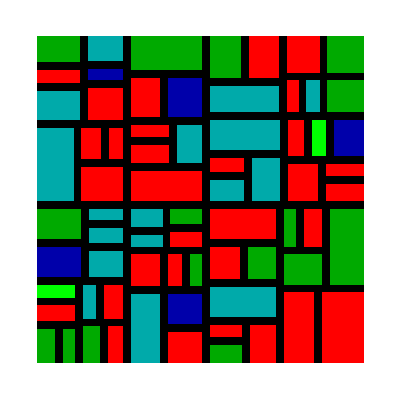

```mathematica
ArrayPlot[mapGrid,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False]
```

## Spawn Entities on City Blocks

Now that we have all our blocks figured out, we want to design entities(buildings, trees, etc.) to add to our city in order to complete it.

First we define the colors we want to use and map it to numbers using Associations. We want to make sure we keep the color scheme we used for the blocks before.

Create a list of colors and map a number to each color:

```mathematica
colors={White,Black,Gray,Green,Red,Darker[Green],Darker[Blue],Darker[Cyan],Cyan,Blue,Darker[Brown],Brown,Darker[Gray]};
colorData=Thread[Range[0,(colors//Length)-1]->colors];
```

Next, to create a 3D model of our city, we need to create a 3D grid. We will keep our original mapGrid as the city’s base and add 2D grids of 0 which have the same dimension as mapGrid. In this case we will add 40 of these empty 2D grids making our city 50 units tall.

Create an empty 3D model of our city with the mapGrid as the base:

```mathematica
emptymapGrid=Table[0,{x,mapGrid//Length},{y,mapGrid[[1]]//Length}];
city3D=Prepend[Table[emptymapGrid,49],mapGrid];
```

#### Defining the entities

Since we defined the colors, we can now “draw” our entities. We do this by creating 3D matrices filled with the numbers that map to colors.

```mathematica
tree=;
house=;
apartment=;
factory=;
skyscraper=;
```

ArrayPlot3D will convert these matrices using colorData into colored pixels creating the visual of our entities.
Here is an example of the skyscraper:

Visual of the skyscraper:

```mathematica
ArrayPlot3D[skyscraper,ColorRules->colorData]
```

-Graphics3D-

### populating blocks with entities(buildings and trees)

We can now start adding the entities to the city :D.

Here will we create lists for each type of block with the types of entities they will contain. This makes it possible to add more entities in the future and easily customize what types of entities each block will contain.

Adding entities to a list for each block type:

```mathematica
parkEntities={tree};
residentialEntities={apartment,house};
businessEntities={skyscraper};
industrialEntities={factory};
commercialEntities={skyscraper};
```

To make it easy to access these lists from the number of the block stored in mapGrid, we create an association.

Create an association between the number of a block to the list of entities that block contains:

```mathematica
blockEntities={parkEntities,residentialEntities,industrialEntities,commercialEntities,businessEntities};
numToEntity=AssociationThread[{3,4,5,6,7},blockEntities];
```

To add each entity, we essentially replace a 3D area of the mapGrid3D with the definition of the entity.

Function that will take in coordinates of where the entity will be added and the entity and adds it:

```mathematica
putEntity[coords_,entity_]:=Module[{x1=coords[[1]],y1=coords[[2]]},city3D[[2;;2+(entity//Length)-1,x1;;x1+(entity[[1]]//Length)-1,y1;;y1+(entity[[1,1]]//Length)-1]]=entity;];
```

Now for the process of adding entities, we will iterate through every cell in the 2D area of a block and check if there space for the entity. If there is, there is a 22% chance it will add the entity(can be changed):

Function that takes in the coordinates of a block and an entity, iterates through the 2D space of a block and adds an entity at a 22% rate if there is space:

```mathematica
spawnEntities[coords_,entity_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]],z=3,bigBlockZero=Table[0,{(entity[[1]]//Length)},{(entity[[1,1]]//Length)}]},
Table[
If[
bigBlockZero==city3D[[z]][[i;;i+(entity[[1]]//Length)-1,j;;j+(entity[[1,1]]//Length)-1]]&&RandomReal[]<=0.22,
putEntity[{i,j},entity],0],
{i,x1,x2-(entity//Length),RandomInteger[{2,3}]},{j,y1,y2-(entity[[1]]//Length),RandomInteger[{entity[[1]][[1]]//Length,(entity[[1]][[1]]//Length)+1}]}];]
```

Finally, we apply the above function to each block. When iterating through the block, we move a random increment in order to add variation in the position of the entities.

Use the spawnEntity[] function on every block, randomly choosing how much cells we move while iterating

```mathematica
Table[spawnEntities[zeroBlocks[[i]],RandomChoice[numToEntity[mapGrid[[zeroBlocks[[i,1]],zeroBlocks[[i,2]]]]]]],{i,zeroBlocks//Length}];
```

Something that can be noticed is that some of the entities combine to make bigger entities which can be pretty cool but doesn’t always look the most natural.

## Final Results

### City Visualization

Using ArrayPlot3D we can now visualize our populated city.

Visualize city3D:

```mathematica
ArrayPlot3D[city3D,ColorRules->colorData,BoxRatios->{1, 1,0.25}]
```

-Graphics3D-

## Conclusion & Future work

Perlin noise is a tool that is used commonly in many aspects of video generation. This project shows how it can be applied to many aspects of generation for a single map.

For future improvements, the entity generation as well as the block classification can be made more realistic through testing different numbers. Another idea I wanted to implement was this option for users to be able to customize the generation of the city further such as choosing the percentage density of certain block types or entities.

## Acknowledgements

I would like to thank my mentor, Felipe Amorim, and my TAs Ethan Kong and Gregory Roudenko for helping and supporting me on this project.

## Works Cited

Flafla2. (2014, August 9). Understanding Perlin Noise. adrian’s soapbox. https://adrianb.io/2014/08/09/perlinnoise.html

Spottedleaf. (n.d.). OldGenerator (Version master) [Computer software]. GitHub. Retrieved July 3, 2025, from https://github.com/Spottedleaf/OldGenerator/

The Worldsmith Project. (2024, June 22). An algorithm for city map generation. https://zero.re/worldsmith/roadnet/

The Worldsmith Project. (2024, August 21). Block assignment: Using adjacency tables. https://zero.re/worldsmith/blockassign/

Noise generator. (n.d.). In Minecraft Wiki. Fandom. Retrieved July 5, 2025, from https://minecraft.fandom.com/wiki/Noise_generator

Perlin, K. (n.d.). Perlin noise. NYU Media Research Laboratory. Retrieved July 3, 2025, from https://mrl.cs.nyu.edu/~perlin/noise/

Perlin, K. (2002). Improving noise. ACM Transactions on Graphics, 21(3), 681–682. https://doi.org/10.1145/566654.566636